```mathematica
α[i_]:=BesselJZero[1, i]
```

```mathematica
α[0]:=0
```

```mathematica
mat[Nmax_,S_?NumericQ]:=Table[N[2/S BesselJ[0,1/S α[i]α[j]]/(Abs[BesselJ[0,α[i]]]Abs[BesselJ[0,α[j]]]),30],{i,0,Nmax},{j,0,Nmax}]
```

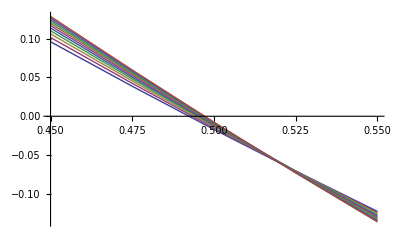

```mathematica
ListLinePlot[Table[{z,Det[mat[Nmax,α[Nmax]+z (α[Nmax+1]-α[Nmax])]]-1},{Nmax,5,15},{z,0.45,0.55,1/40}]]
```

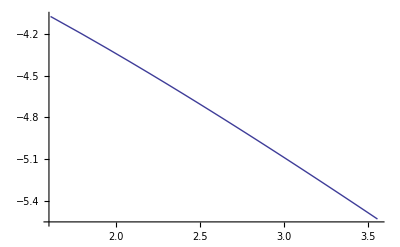

```mathematica
ListLinePlot[Table[{Log[Nmax],Log[Abs[Det[mat[Nmax,(α[Nmax]+α[Nmax+1])/2]]-1]]},{Nmax,5,35}]]
```

```mathematica
BesselJZero[1,Nmax+1]BesselJZero[1,j]
```

```mathematica
Normal[LinearModelFit[Table[{Log[2^Nmax],Log[(2^Nmax)^3]},{Nmax,3,7}],x,x]]
```

-7.94411×10^-15+3. x

```mathematica
N[Exp[1]]
```

2.71828

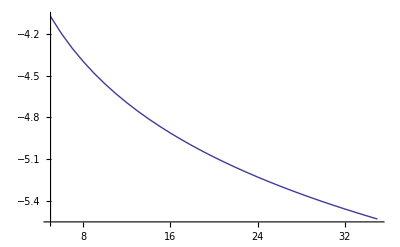

```mathematica
ListLinePlot[Table[{Nmax,Log[Abs[Det[mat[Nmax,(α[Nmax]+α[Nmax+1])/2]]-1]]},{Nmax,5,35}]]
```

```mathematica
Abs[Det[mat[64,BesselJZero[0,65]]]-1]
```

0.00503639817144787006817339462

```mathematica
Table[N[BesselJZero[0,i],30],{i,1,5}]
```

{2.40482555769577276862163187933,5.52007811028631064959660411281,8.65372791291101221695419871266,11.7915344390142816137430449119,14.9309177084877859477625939974}

```mathematica
Table[N[BesselJZero[1,i],30],{i,1,5}]
```

{3.83170597020751231561443588631,7.01558666981561875353704998148,10.1734681350627220771857117768,13.3236919363142230323936841269,16.470630050877632812552460471}

```mathematica
Table[N[BesselJZero[2,i],30],{i,1,5}]
```

{5.13562230184068255630140169014,8.41724414039986485778361367618,11.6198411721490594270941449868,14.7959517823512607466614713202,17.9598194949878264551151420773}

```mathematica
Table[N[1/2(BesselJZero[1,i]+BesselJZero[1,i+1])-BesselJZero[2,i],30],{i,1,5}]
```

{0.288024018170882978274341243755,0.177283262039305557577767202972,0.128738863539413127695552965107,0.101209211244667175811600978741,0.0834247856851109617236211003098}

```mathematica
Z=mat[32,1/2(α[32]+α[33])];
```

```mathematica
Max[Z. Z - IdentityMatrix[33]]
```

0.001486609056741503648826601

```mathematica
Y[z_]:=mat[32,α[32]+z(α[32]+α[33])]
```

```mathematica
Y[Nmax_,z_]:=mat[Nmax,α[Nmax]+z(α[Nmax+1]-α[Nmax])]
```

```mathematica
ListLinePlot[Table[{z,Max[Abs[Y[32,z].Y[32,z]-IdentityMatrix[33]]]},{z,0.45,0.55,1/200}]]
```

$Aborted

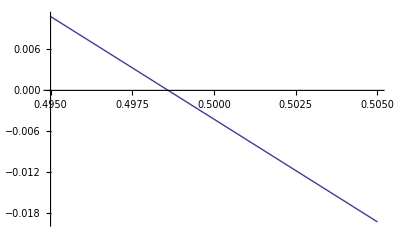

```mathematica
ListLinePlot[Table[{z,Abs[Det[Y[32,z]]]-1},{z,0.495,0.505,1/100}]]
```

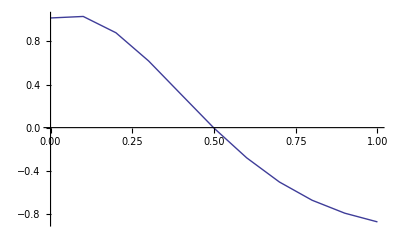

```mathematica
ListLinePlot[Table[{z,Abs[Det[Y[30,z]]]-1},{z,0,1,1/10}]]
```

```mathematica
Normal[LinearModelFit[Table[{z,Abs[Det[Y[32,z]]]-1},{z,0.495,0.505,1/100}],x,x]]
```

1.50077-3.00999 x

```mathematica
Solve[1.50077422079091-3.009985411624585 x==0,x]
```

{{x→0.498599}}

```mathematica
FindRoot[Abs[Det[Y[32,z]]]-1,{z,1/2}]
```

{z→0.498584}

```mathematica
Abs[Det[Y[32,0.4985985031671281]]]-1
```

-0.0000427654

```mathematica
Abs[Det[Y[32,0.4985843204381852]]]-1
```

-9.63674×10^-14

```mathematica
Abs[Det[mat[32,1/2(BesselJZero[1,32]+BesselJZero[1,33])]]]-1
```

-0.00426504769806839336974070089

```mathematica
Table[{Nmax,FindRoot[Abs[Det[Y[Nmax,z]]]-1,{z,1/2}][[1,2]]},{Nmax,1,15}]
```

{{1,0.477328},{2,0.484616},{3,0.488439},{4,0.490748},{5,0.492289},{6,0.493389},{7,0.494213},{8,0.494854},{9,0.495367},{10,0.495786},{11,0.496136},{12,0.496431},{13,0.496685},{14,0.496904},{15,0.497097}}

```mathematica
Table[{Nmax,FindRoot[Abs[Det[Y[Nmax,z]]]-1,{z,1/2}][[1,2]]},{Nmax,1,33}]
```

{{1,0.477328},{2,0.484616},{3,0.488439},{4,0.490748},{5,0.492289},{6,0.493389},{7,0.494213},{8,0.494854},{9,0.495367},{10,0.495786},{11,0.496136},{12,0.496431},{13,0.496685},{14,0.496904},{15,0.497097},{16,0.497266},{17,0.497417},{18,0.497552},{19,0.497674},{20,0.497784},{21,0.497884},{22,0.497975},{23,0.498059},{24,0.498136},{25,0.498207},{26,0.498273},{27,0.498334},{28,0.498391},{29,0.498444},{30,0.498494},{31,0.49854},{32,0.498584},{33,0.498626}}

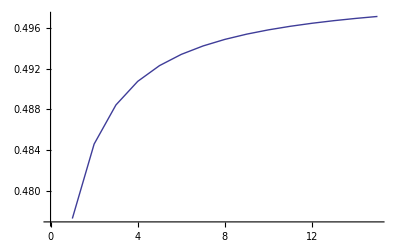

```mathematica
ListLinePlot[Out[73]]
```

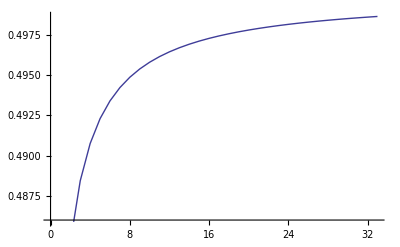

```mathematica
ListLinePlot[Out[75]]
```